# Notebook for : Scattering From Black Holes by Futterman, Handler & Matzner

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
January 29, 2021

## REMEMBER!!!! Computer Algebra Doesn’t Like Sin[θ] Use z instead!!!!

```mathematica
Hyperlink["bhpt seminar" , "https://www.youtube.com/watch?v=9jHxs4HiMSg"]
(* IMPORTANT!!!! use substituion z = Cos[θ] as mentioned in bhpt seminar so calculations go easier!!!! *) 
(* Day 1 Video 2:44 mark *)
```

[bhpt seminar](https://www.youtube.com/watch?v=9jHxs4HiMSg)

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book

```mathematica
Hyperlink["Scattering From Black Holes Matzner & futterman","https://www.cambridge.org/us/academic/subjects/physics/cosmology-relativity-and-gravitation/scattering-black-holes?format=PB&isbn=9780521112109"]
```

[Scattering From Black Holes Matzner & futterman](https://www.cambridge.org/us/academic/subjects/physics/cosmology-relativity-and-gravitation/scattering-black-holes?format=PB&isbn=9780521112109)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 4 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Notation and Replace Rules

```mathematica
Clear[deltaSigmaZfunction]
deltaSigmaZfunction = { 
Δ->   Δ[r] , 
Σ->   Σ[r,θ] , 
z->   z[θ]
} ;
deltaSigmaZfunction  // TableForm
```

Δ→Δ[r]
Σ→Σ[r,θ]
z→z[θ]

```mathematica
Clear[zReplace]
zReplace = { 
Sin[θ] -> z[θ] , 
Cos[θ] -> √(1-z[θ]^2)
} ;
zReplace // TableForm
```

Sin[θ]→z[θ]
Cos[θ]→√(1-z[θ]^2)

```mathematica
Clear[SinThetaReplace]
SinThetaReplace = {
 z[θ]-> Sin[θ] , 
 z'[θ]-> Cos[θ] , 
 z''[θ]-> -Sin[θ]
} ;
SinThetaReplace  // TableForm
```

z[θ]→Sin[θ]
z'[θ]→Cos[θ]
z''[θ]→-Sin[θ]

```mathematica
Clear[deltaSigmaZreplace]
deltaSigmaZreplace = { 
 Δ[r]==  r^2-2 M r + a^2 , 
Σ[r,θ]==  r^2+ a^2 Cos[θ]^2 
}  /. zReplace ;
deltaSigmaZreplace  // TableForm
```

Δ[r]==a^2-2 M r+r^2
Σ[r,θ]==r^2+a^2 (1-z[θ]^2)

```mathematica
Clear[kerrSimplifyRules]
kerrSimplifyRules=DeleteCases[DeleteCases[Flatten[ {
D[deltaSigmaZreplace,r] , 
D[deltaSigmaZreplace,θ] , 
D[deltaSigmaZreplace,{r,2}] , 
D[deltaSigmaZreplace,{θ,2}] , 
D[D[deltaSigmaZreplace,r],θ]
}] ,True,Infinity],0] /. Equal-> Rule ;
kerrSimplifyRules // TableForm // pdConv
```

(∂Δ(r))/(∂r)→2 r-2 M
(∂Σ(r,θ))/(∂r)→2 r
(∂Σ(r,θ))/(∂θ)→-2 a^2 z(θ) (∂z(θ))/(∂θ)
(∂^2 Δ(r))/(∂r^2)→2
(∂^2 Σ(r,θ))/(∂r^2)→2
(∂^2 Σ(r,θ))/(∂θ^2)→a^2 (-2 z(θ) (∂^2 z(θ))/(∂θ^2)-2 ((∂z(θ))/(∂θ))^2)
(∂^2 Σ(r,θ))/(∂r ∂θ)→0

```mathematica
kerrSimplifyRules /. SinThetaReplace // Expand // Simplify // TableForm // pdConv
```

(∂Δ(r))/(∂r)→2 r-2 M
(∂Σ(r,θ))/(∂r)→2 r
(∂Σ(r,θ))/(∂θ)→-2 a^2 sin(θ) cos(θ)
(∂^2 Δ(r))/(∂r^2)→2
(∂^2 Σ(r,θ))/(∂r^2)→2
(∂^2 Σ(r,θ))/(∂θ^2)→-2 a^2 cos(2 θ)
(∂^2 Σ(r,θ))/(∂r ∂θ)→0

## Line Element and Metric 2.18 Page 16 (If Sin[θ] goes to z - need to change dθ? )

```mathematica
Clear[eq2pt18]
eq2pt18 = 
(-(1-(2 M r)/Σ) dt^2 - ( 4 M a r (Sin[θ]^2/Σ)) dt dϕ + (Σ/Δ) dr^2 +Σ dθ^2+ Sin[θ]^2 ( r^2+ a^2+ 2 M a^2 r (Sin[θ]^2/Σ)) dϕ^2 )/. Sin[θ]-> z
```

dt^2 (-1+(2 M r)/Σ)+dϕ^2 z^2 (a^2+r^2+(2 a^2 M r z^2)/Σ)-(4 a dt dϕ M r z^2)/Σ+dθ^2 Σ+(dr^2 Σ)/Δ

```mathematica
Clear[metric2pt18a]
metric2pt18a = 
lineToMetric[ eq2pt18 , {dt,dr,dθ,dϕ}] ;
metric2pt18a // MatrixForm
```

(-1+(2 M r)/Σ | 0 | 0 | -(2 a M r z^2)/Σ
0 | Σ/Δ | 0 | 0
0 | 0 | Σ | 0
-(2 a M r z^2)/Σ | 0 | 0 | z^2 (a^2+r^2+(2 a^2 M r z^2)/Σ))

```mathematica
Clear[metric2pt18]
metric2pt18 = 
metric2pt18a /. deltaSigmaZfunction   ;
metric2pt18 // MatrixForm
```

(-1+(2 M r)/Σ[r,θ] | 0 | 0 | -(2 a M r z[θ]^2)/Σ[r,θ]
0 | Σ[r,θ]/Δ[r] | 0 | 0
0 | 0 | Σ[r,θ] | 0
-(2 a M r z[θ]^2)/Σ[r,θ] | 0 | 0 | z[θ]^2 (a^2+r^2+(2 a^2 M r z[θ]^2)/Σ[r,θ]))

```mathematica
Clear[inverse2pt18]
inverse2pt18 = 
Inverse[ metric2pt18 ] // Expand // Simplify  ;
inverse2pt18 // MatrixForm
```

(-(2 a^2 M r z[θ]^2+(a^2+r^2) Σ[r,θ])/(2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r,θ])) | 0 | 0 | -(2 a M r)/(2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r,θ]))
0 | Δ[r]/Σ[r,θ] | 0 | 0
0 | 0 | 1/Σ[r,θ] | 0
-(2 a M r)/(2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r,θ])) | 0 | 0 | (-2 M r+Σ[r,θ])/(2 a^2 M r z[θ]^4-(a^2+r^2) z[θ]^2 (2 M r-Σ[r,θ])))

```mathematica
metric2pt18 . inverse2pt18 // Expand // Simplify // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
inverse2pt18  . metric2pt18// Expand // Simplify // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Tensors Calculated From The Kerr Metric

```mathematica
$CacheTensorValues=True;
```

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] (*  , ActWithNested-> Simplify  *) ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] (*  , ActWith-> Simplify  *) ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] (*  , ActWith-> Simplify *)  ] ;
 tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]]  (* , ActWith-> Simplify *) ] ; 
 tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]]  (* , ActWith-> Simplify *) ] ;  
  tensorList[[8]] = 
WeylTensor[ tensorList[[1]] (*   , ActWith-> Simplify  *) ] ; 
 tensorList[[9]] = 
CottonTensor[ tensorList[[1]]  (*  , ActWith-> Simplify *) ] ;
];
```

```mathematica
(*  IMPORTANT!!! Comment out  ActWith-> Simplify and turn on Cacheing to get this timing otherwise it takes forever *) 
(*  Last timing took 23.51 to calculate all tensors *) 
input[ "metric2pt18", metric2pt18, "Kerr","g^Kerr",{t,r,θ,ϕ}, "Greek"] // Timing
```

{23.5036,Null}

```mathematica
tensorList
```

{(g^Kerr)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList[[1]]
TensorName[tensorList[[1]]]
TensorValues[tensorList[[1]]] // MatrixForm
```

(g^Kerr)_αβ^

Kerr

(-1+(2 M r)/Σ[r] | 0 | 0 | -(2 a M r z[θ]^2)/Σ[r]
0 | Σ[r]/Δ[r] | 0 | 0
0 | 0 | Σ[r] | 0
-(2 a M r z[θ]^2)/Σ[r] | 0 | 0 | z[θ]^2 (a^2+r^2+(2 a^2 M r z[θ]^2)/Σ[r]))

```mathematica
tensorList[[2]]
TensorName[tensorList[[2]]]
TensorValues[tensorList[[2]]] // MatrixForm
```

Γ_βγ^α

ChristoffelSymbolKerr

((0
(M (a^2+r^2) (-Σ[r]+r Σ'[r]))/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])
(4 a^2 M^2 r^2 z[θ] z'[θ])/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])
0) | ((M (a^2+r^2) (-Σ[r]+r Σ'[r]))/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])
0
0
(a M z[θ]^2 ((a^2-r^2) Σ[r]-r (a^2+r^2) Σ'[r]))/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])) | ((4 a^2 M^2 r^2 z[θ] z'[θ])/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])
0
0
-(4 a^3 M^2 r^2 z[θ]^3 z'[θ])/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])) | (0
(a M z[θ]^2 ((a^2-r^2) Σ[r]-r (a^2+r^2) Σ'[r]))/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])
-(4 a^3 M^2 r^2 z[θ]^3 z'[θ])/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])
0)
(-(M Δ[r] (Σ[r]-r Σ'[r]))/Σ[r]^3
0
0
(a M z[θ]^2 Δ[r] (Σ[r]-r Σ'[r]))/Σ[r]^3) | (0
1/2 (-Δ'[r]/Δ[r]+Σ'[r]/Σ[r])
0
0) | (0
0
-(Δ[r] Σ'[r])/(2 Σ[r])
0) | ((a M z[θ]^2 Δ[r] (Σ[r]-r Σ'[r]))/Σ[r]^3
0
0
-(z[θ]^2 Δ[r] (r Σ[r]^2+a^2 M z[θ]^2 (Σ[r]-r Σ'[r])))/Σ[r]^3)
(0
0
0
(2 a M r z[θ] z'[θ])/Σ[r]^2) | (0
0
Σ'[r]/(2 Σ[r])
0) | (0
Σ'[r]/(2 Σ[r])
0
0) | ((2 a M r z[θ] z'[θ])/Σ[r]^2
0
0
-((4 a^2 M r z[θ]^3+(a^2+r^2) z[θ] Σ[r]) z'[θ])/Σ[r]^2)
(0
(a M (-Σ[r]+r Σ'[r]))/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])
-(2 a M r z[θ] (-2 M r+Σ[r]) z'[θ])/((2 a^2 M r z[θ]^4-(a^2+r^2) z[θ]^2 (2 M r-Σ[r])) Σ[r])
0) | ((a M (-Σ[r]+r Σ'[r]))/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])
0
0
((-2 M r^2+a^2 M z[θ]^2) Σ[r]+r Σ[r]^2-a^2 M r z[θ]^2 Σ'[r])/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])) | (-(2 a M r z[θ] (-2 M r+Σ[r]) z'[θ])/((2 a^2 M r z[θ]^4-(a^2+r^2) z[θ]^2 (2 M r-Σ[r])) Σ[r])
0
0
((-((a^2+r^2) (2 M r-Σ[r]) Σ[r])+4 a^2 M r z[θ]^2 (-M r+Σ[r])) z'[θ])/(z[θ] (2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])) | (0
((-2 M r^2+a^2 M z[θ]^2) Σ[r]+r Σ[r]^2-a^2 M r z[θ]^2 Σ'[r])/((2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])
((-((a^2+r^2) (2 M r-Σ[r]) Σ[r])+4 a^2 M r z[θ]^2 (-M r+Σ[r])) z'[θ])/(z[θ] (2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r])) Σ[r])
0))

```mathematica
(* Output long and boring.. *)
tensorList[[3]]
TensorName[tensorList[[3]]]
(* TensorValues[tensorList[[3]]] // MatrixForm *)
```

R_αβγδ^

RiemannTensorKerr

```mathematica
tensorList[[4]]
TensorName[tensorList[[4]]]
(* TensorValues[tensorList[[4]]] // MatrixForm *)
```

R_βγ^

RicciTensorKerr

```mathematica
tensorList[[5]]
TensorName[tensorList[[5]]]
(* TensorValues[tensorList[[5]]] *) 

( TensorValues[tensorList[[5]]] //.   kerrSimplifyRules   // Expand  // Simplify  ) 
( TensorValues[tensorList[[5]]] //.   kerrSimplifyRules   // Expand  // Simplify  )  //. M-> 0 
( TensorValues[tensorList[[5]]] //.   kerrSimplifyRules   // Expand  // Simplify  )  //. a-> 0
```

R

RicciScalarKerr

-(8 a^2 (a^6-2 a^4 M r+2 a^4 r^2-a^2 M^2 r^2+a^2 r^4-4 M^2 r^4+2 M r^5+(a^2+r^2) (a^4+3 a^2 r^2+2 r^2 (-2 M^2-M r+r^2)) Cos[2 θ]+a^2 M r (2 a^2-3 M r+2 r^2) Cos[4 θ]))/((a^2+r (-2 M+r))^2 (a^2+2 r^2+a^2 Cos[2 θ])^3)

-(8 a^2 (a^6+2 a^4 r^2+a^2 r^4+(a^2+r^2) (a^4+3 a^2 r^2+2 r^4) Cos[2 θ]))/((a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ])^3)

0

```mathematica
tensorList[[5]]
TensorName[tensorList[[5]]]

( TensorValues[tensorList[[5]]]  //.   kerrSimplifyRules   // Expand  // Simplify  )//. M-> 0 
(( TensorValues[tensorList[[5]]]  //.   kerrSimplifyRules   // Expand  // Simplify  )//. M-> 0  ) /. a-> 0
```

R

RicciScalarKerr

-(8 a^2 (a^6+2 a^4 r^2+a^2 r^4+(a^2+r^2) (a^4+3 a^2 r^2+2 r^4) Cos[2 θ]))/((a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ])^3)

0

```mathematica
tensorList[[6]]
TensorName[tensorList[[6]]]
(* TensorValues[tensorList[[6]]] *)
```

K

KretschmannScalarKerr

```mathematica
tensorList[[7]]
TensorName[tensorList[[7]]]
(* TensorValues[tensorList[[7]]] // MatrixForm *)
```

G_αβ^

EinsteinTensorKerr

```mathematica
tensorList[[8]]
TensorName[tensorList[[8]]]
(* TensorValues[ tensorList[[8]] ] // MatrixForm *)
```

C_αβγδ^

WeylTensorKerr

```mathematica
tensorList[[9]]
TensorName[tensorList[[9]]]
(* TensorValues[tensorList[[9]]] // MatrixForm *)
```

C_αβγ^

CottonTensorKerr

## Null Tetrad Construction and Check of Completeness and Orthogonality

```mathematica
Clear[ℓ] /. ΔofrReplace 
ℓ = {(r^2+a^2)/Δ,1,0,a/Δ}/. deltaSigmaZfunction
```

ReplaceAll::reps: {ΔofrReplace} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Null/.ΔofrReplace

{(a^2+r^2)/Δ[r],1,0,a/Δ[r]}

```mathematica
Clear[𝓃]
𝓃 = 1/(2(r^2+a^2 Cos[θ]^2)){ r^2+a^2,-Δ,0,a} /.  Sin[θ]-> z /. Cos[θ]-> √(1-z^2) /. deltaSigmaZfunction
```

{(a^2+r^2)/(2 (r^2+a^2 (1-z[θ]^2))),-Δ[r]/(2 (r^2+a^2 (1-z[θ]^2))),0,a/(2 (r^2+a^2 (1-z[θ]^2)))}

```mathematica
Clear[𝓂]
𝓂 = 
1/(√2(r+ⅈ a Cos[θ])){ ⅈ a Sin[θ],0,1,ⅈ/Sin[θ]} /. Sin[θ]-> z  /. Cos[θ]-> √(1-z^2)  /. deltaSigmaZfunction
```

{(ⅈ a z[θ])/(√2 (r+ⅈ a √(1-z[θ]^2))),0,1/(√2 (r+ⅈ a √(1-z[θ]^2))),(ⅈ Csc[θ])/(√2 (r+ⅈ a √(1-z[θ]^2)))}

```mathematica
Clear[𝓂bar]
𝓂bar = 
1/(√2(r-ⅈ a Cos[θ])){- ⅈ a Sin[θ],0,1,-ⅈ/Sin[θ]}/. Sin[θ]-> z/. Cos[θ]-> √(1-z^2)  /. deltaSigmaZfunction
```

{-(ⅈ a z[θ])/(√2 (r-ⅈ a √(1-z[θ]^2))),0,1/(√2 (r-ⅈ a √(1-z[θ]^2))),-(ⅈ Csc[θ])/(√2 (r-ⅈ a √(1-z[θ]^2)))}

```mathematica
(* Always check if indices needed are up or down *) 
l = ToTensor[ {"NewTensor" , "l"} , tensorList[[1]] , ℓ , {μ}]
n = ToTensor[{"NewTensor" , "n" } , tensorList[[1]] , 𝓃 , {μ} ] 
m = ToTensor[{"NewTensor" , "m" } , tensorList[[1]] , 𝓂 , {μ} ] 
mbar = ToTensor[{"NewTensor" , "mbar" } , tensorList[[1]] , 𝓂bar , {μ} ]
```

l_^μ

n_^μ

m_^μ

mbar_^μ

```mathematica
TensorValues[ContractIndices[l[-μ]l[μ]]] == 0  /.( deltaSigmaZreplace   /. Equal-> Rule )  // Expand // FullSimplify 
TensorValues[ContractIndices[n[-μ]n[μ]] ]== 0  /. ( deltaSigmaZreplace   /. Equal-> Rule ) // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]m[μ]]] == 0   /. ( deltaSigmaZreplace   /. Equal-> Rule )   // Expand // FullSimplify 
TensorValues[ContractIndices[mbar[-μ]mbar[μ]]] == 0  /. ( deltaSigmaZreplace   /. Equal-> Rule )   // Expand // FullSimplify 
TensorValues[ContractIndices[l[-μ]n[μ]]] == -1/.( deltaSigmaZreplace   /. Equal-> Rule )   // Expand // FullSimplify 
TensorValues[ContractIndices[l[μ]n[-μ]]] ==- 1  /.( deltaSigmaZreplace   /. Equal-> Rule )  // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]mbar[μ]]] == 1 /.( deltaSigmaZreplace   /. Equal-> Rule )  // Expand // FullSimplify 
TensorValues[ContractIndices[m[μ]mbar[-μ]]] == 1 /.( deltaSigmaZreplace   /. Equal-> Rule )  // Expand // FullSimplify 

Clear[completenessDownIndices]
completenessDownIndices = 
MergeTensors[-l[-μ]n[-ν]-n[-μ]l[-ν] + m[-μ]mbar[-ν]+ m[-ν]mbar[-μ]]  ;
TensorValues[ completenessDownIndices ]   // Expand //. kerrSimplifyRules // FullSimplify // MatrixForm

Thread[Flatten[metric2pt18] == 
Flatten[ TensorValues[ completenessDownIndices ]] ] // Expand // FullSimplify  // TableForm

Clear[completenessUpIndices]
completenessUpIndices = 
MergeTensors[-l[μ]n[ν]-n[μ]l[ν] + m[μ]mbar[ν]+ m[ν]mbar[μ]]  ;
TensorValues[ completenessUpIndices ]   // Expand // FullSimplify // MatrixForm

Thread[Flatten[inverse2pt18] == 
Flatten[ TensorValues[ completenessUpIndices ]] ]  // Expand  /.( deltaSigmaZreplace   /. Equal-> Rule )  // Expand // FullSimplify  // TableForm
```

((-a^2-r^2+a^2 Sin[θ]^2+Σ[r]) (M r (a^2+2 r^2+a^2 Cos[2 θ])-(a^2+r (-2 M+r)) Σ[r]))/((a^2+r (-2 M+r)) Σ[r])==0

1+(2 M r)/(a^2-2 M r+r^2)+(2 Σ[r])/(a^2+2 r^2+a^2 Cos[2 θ])==(M r (a^2+2 r^2+a^2 Cos[2 θ]))/((a^2+r (-2 M+r)) Σ[r])

True

True

3+(2 M r)/(a^2-2 M r+r^2)+(2 Σ[r])/(a^2+2 r^2+a^2 Cos[2 θ])==(M r (a^2+2 r^2+a^2 Cos[2 θ]))/((a^2+r (-2 M+r)) Σ[r])

((-a^2-r^2+a^2 Sin[θ]^2+Σ[r]) (-M r (a^2+2 r^2+a^2 Cos[2 θ])+(a^2+r (-2 M+r)) Σ[r]))/((a^2+r (-2 M+r))^2 Σ[r])==1

False

False

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(2 M r)/Σ[r,θ]==1
True
True
(a M r z[θ])/Σ[r,θ]==0
True
Σ[r,θ]/Δ[r]==0
True
True
True
True
Σ[r,θ]==0
True
(a M r z[θ])/Σ[r,θ]==0
True
True
z[θ] (a^2+r^2+(2 a^2 M r z[θ]^2)/Σ[r,θ])==0

((-(a^2+r^2)^2+a^2 z[θ]^2 Δ[r])/((a^2+r^2-a^2 z[θ]^2) Δ[r]) | 0 | 0 | -(a (a^2+r^2-Csc[θ] z[θ] Δ[r]))/((a^2+r^2-a^2 z[θ]^2) Δ[r])
0 | Δ[r]/(a^2+r^2-a^2 z[θ]^2) | 0 | 0
0 | 0 | 1/(a^2+r^2-a^2 z[θ]^2) | 0
-(a (a^2+r^2-Csc[θ] z[θ] Δ[r]))/((a^2+r^2-a^2 z[θ]^2) Δ[r]) | 0 | 0 | (-a^2+Csc[θ]^2 Δ[r])/((a^2+r^2-a^2 z[θ]^2) Δ[r]))

(2 M r)/(2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r,θ]))==(a^2+r^2-Δ[r])/((a^2+r^2-a^2 z[θ]^2) Δ[r])
True
True
(2 a M r)/(2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r,θ]))==(a (a^2+r^2-Csc[θ] z[θ] Δ[r]))/((a^2+r^2-a^2 z[θ]^2) Δ[r])
True
Δ[r]/Σ[r,θ]==Δ[r]/(a^2+r^2-a^2 z[θ]^2)
True
True
True
True
a^2 z[θ]^2+Σ[r,θ]==a^2+r^2
True
(2 a M r)/(2 a^2 M r z[θ]^2-(a^2+r^2) (2 M r-Σ[r,θ]))==(a (a^2+r^2-Csc[θ] z[θ] Δ[r]))/((a^2+r^2-a^2 z[θ]^2) Δ[r])
True
True
(-2 M r+Σ[r,θ])/(2 a^2 M r z[θ]^4-(a^2+r^2) z[θ]^2 (2 M r-Σ[r,θ]))==(-a^2+Csc[θ]^2 Δ[r])/((a^2+r^2-a^2 z[θ]^2) Δ[r])

```mathematica
(* Most Important: See Chandra page 37, 38 as to how not to use covaraint derivatives, these are entirely too messy  *)
```

See if page 11 Exact Space-Times can be implemented
McMahon page 199
Carmeli Classical Fields page 391, page 186
Frolov & Novikov Appendix 
D’Eath page 52
Hawking & Israel page 385, IMPORTANT page 400
Ludvigson page 210
D’Inverno IMPORTANT page 250

## Calculation of Newman Penrose Quantities: Spin Coefficients , Ricci Scalars , Weyl Scalars

Convention for spin coefficients taken from “Colliding Planes Waves” by J.B. Griffiths Page 8 Equation 2.12.   The order listed is done in such a way that it matches the list NPSpinCoefficients[Dyad] when evaluated in xAct

```mathematica
Clear[spinCoefficientReplace] 
spinCoefficientReplace= {
α-> ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ] mbar[ν]] // TensorValues )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] mbar[ν]] // TensorValues)) ) , 
β -> 
((1/2)((MergeTensors[ CovariantD[ l[-μ],-ν] n[μ]m[ν]] // TensorValues)- 
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] m[ν]] // TensorValues ))),
γ -> (* something weird here correct definition off by minus sign *) ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ]n[ν] ] // TensorValues  // Expand  )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] n[ν]] // TensorValues // Expand  // FullSimplify )) // Expand ) , 
ε -> ( (1/2)(( MergeTensors[CovariantD[l[-μ],-ν] n[μ] l[ν]] // TensorValues  // Expand  // FullSimplify  )  - 
(MergeTensors[ CovariantD[ m[-μ],-ν] mbar[μ] l[ν]] // TensorValues // Expand // FullSimplify) ) // Expand  // FullSimplify ) , 
κ->(  MergeTensors[ CovariantD[ l[-μ] ,-ν] m[μ] l[ν]  ]  // TensorValues ) , 
λ-> (* note minus sign *)(-1)*( MergeTensors[ CovariantD[ n[-μ],-ν] mbar[μ] mbar[ν] ]  // TensorValues // Expand // FullSimplify)  ,
μ-> (*note minus sign *)(-1)*( MergeTensors [ CovariantD[ n[-μ] , -ν ] mbar[μ] m[ν] ] // TensorValues  // Expand  // FullSimplify )  , 
ν-> ( MergeTensors[ CovariantD[ n[-μ],-ν]m[μ] n[ν] ] // TensorValues ) , 
π-> (* Note minus sign *)(-1)* (MergeTensors[CovariantD[ n[-μ],-ν] mbar[μ] l[ν]] // TensorValues  // Expand ) , 
ρ ->(  MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] mbar[ν] ] // TensorValues  // Expand // FullSimplify )  , σ->( MergeTensors[ CovariantD[l[-μ] , -ν] m[μ] m[ν]] // TensorValues  // Expand // FullSimplify)  , 
τ->( MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] n[ν ]]// TensorValues )   
} ;
```

```mathematica
spinCoefficientReplace    //. kerrSimplifyRules   // Expand // Simplify // TableForm
```

α→(a (2 r (a^2+r (-2 M+r))+ⅈ a (a^2+r (-4 M+r)) Cos[θ]) Sin[θ])/(4 √2 (a^2+r (-2 M+r)) (-ⅈ r+a Cos[θ]) (ⅈ r+a Cos[θ])^2)
β→((a^2+2 r^2+a^2 Cos[2 θ])^2 (2 ⅈ (a^2+2 r^2) (a^2+r (-2 M+r))+2 ⅈ a^2 (a^2+r (-2 M+r)) Cos[2 θ]+√2 a (2 r (a^2-2 M r+r^2)-ⅈ a (a^2-4 M r+r^2) Cos[θ]) Sin[θ]))/(32 (a^2+r (-2 M+r)) (r+ⅈ a Cos[θ])^4 (ⅈ r+a Cos[θ])^3)
γ→((a^2+2 r^2+a^2 Cos[2 θ])^3 (8 a^4 M+8 a^4 r-16 a^2 M^2 r-24 a^2 M r^2+8 a^2 r^3+32 M^2 r^3-16 M r^4+8 a^2 (M-r) (a^2+r (-2 M+r)) Cos[2 θ]+ⅈ √2 a (a^4+8 r^3 (-2 M+r)+a^2 r (-4 M+9 r)) Sin[θ]-2 √2 a^4 r Sin[2 θ]-2 √2 a^2 r^3 Sin[2 θ]+ⅈ √2 a^5 Sin[3 θ]-4 ⅈ √2 a^3 M r Sin[3 θ]+ⅈ √2 a^3 r^2 Sin[3 θ]))/(256 (a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^5)
ε→(ⅈ a^2 (a^2+r (-4 M+r)) Sin[2 θ])/(4 √2 (a^2+r (-2 M+r))^2 (ⅈ r+a Cos[θ]))
κ→-(a^2 (a^2+r (-4 M+r)) Sin[2 θ])/(2 √2 (a^2+r (-2 M+r))^2 (r+ⅈ a Cos[θ]))
λ→0
μ→-1/(r+ⅈ a Cos[θ])
ν→(a (2 r (a^2+r (-2 M+r))+ⅈ a (a^2+r (-4 M+r)) Cos[θ]) Sin[θ])/(2 √2 (a^2+r (-2 M+r)) (-ⅈ r+a Cos[θ])^2 (ⅈ r+a Cos[θ]))
π→(a^2 (a^2+r (-4 M+r)) Sin[2 θ])/(2 √2 (a^2+r (-2 M+r))^2 (r-ⅈ a Cos[θ]))
ρ→1/(r-ⅈ a Cos[θ])
σ→0
τ→(a (2 r (a^2+r (-2 M+r))+ⅈ a (a^2+r (-4 M+r)) Cos[θ]) Sin[θ])/(2 √2 (a^2+r (-2 M+r)) (-ⅈ r+a Cos[θ])^2 (ⅈ r+a Cos[θ]))

```mathematica
Clear[spinCoefficientConjugateReplace]
spinCoefficientConjugateReplace = 
{
ᾱ-> 
((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ] m[ν]] // TensorValues )-
(MergeTensors[CovariantD[ mbar[-μ],-ν] m[μ] m[ν]] // TensorValues)) ) , 
β̄-> 
((1/2)((MergeTensors[ CovariantD[ l[-μ],-ν] n[μ]mbar[ν]] // TensorValues)- 
(MergeTensors[CovariantD[ mbar[-μ],-ν] m[μ] mbar[ν]] // TensorValues ))), 
γ̄-> 
((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ]n[ν] ] // TensorValues  // Expand  )-
(MergeTensors[CovariantD[ mbar[-μ],-ν] m[μ] n[ν]] // TensorValues // Expand  // FullSimplify )) // Expand ) , 
ϵ̄ -> 
( (1/2)(( MergeTensors[CovariantD[l[-μ],-ν] n[μ] l[ν]] // TensorValues  // Expand  // FullSimplify  )  - 
(MergeTensors[ CovariantD[ mbar[-μ],-ν] m[μ] l[ν]] // TensorValues // Expand // FullSimplify) ) // Expand  // FullSimplify ) , 
κ̄-> 
(  MergeTensors[ CovariantD[ l[-μ] ,-ν] mbar[μ] l[ν]  ]  // TensorValues ) , 
λ̄-> 
(* note minus sign *)(-1)*( MergeTensors[ CovariantD[ n[-μ],-ν] m[μ] m[ν] ]  // TensorValues // Expand // FullSimplify)  ,
μ̄-> 
(-1)*( MergeTensors [ CovariantD[ n[-μ] , -ν ] mbar[μ] m[ν] ] // TensorValues  // Expand  // FullSimplify ) , 
ν̄ -> 
( MergeTensors[ CovariantD[ n[-μ],-ν]mbar[μ] n[ν] ] // TensorValues ) , 
π̄-> 
 (* Note minus sign *)(-1)* (MergeTensors[CovariantD[ n[-μ],-ν] m[μ] l[ν]] // TensorValues  // Expand ) ,
ρ̄-> 
(  MergeTensors[ CovariantD[ l[-μ],-ν] mbar[μ] m[ν] ] // TensorValues  // Expand // FullSimplify )  ,
σ̄-> 
( MergeTensors[ CovariantD[l[-μ] , -ν] mbar[μ] mbar[ν]] // TensorValues  // Expand // FullSimplify)  ,
τ̄-> 
( MergeTensors[ CovariantD[ l[-μ],-ν] mbar[μ] n[ν ]]// TensorValues )   
};
```

```mathematica
spinCoefficientConjugateReplace  //. kerrSimplifyRules   // Expand // Simplify // TableForm
```

ᾱ→(a (2 r (a^2+r (-2 M+r))-ⅈ a (a^2+r (-4 M+r)) Cos[θ]) Sin[θ])/(4 √2 (a^2+r (-2 M+r)) (-ⅈ r+a Cos[θ])^2 (ⅈ r+a Cos[θ]))
β̄→((a^2+2 r^2+a^2 Cos[2 θ])^2 (-2 ⅈ (a^2+2 r^2) (a^2+r (-2 M+r))-2 ⅈ a^2 (a^2+r (-2 M+r)) Cos[2 θ]+√2 a (2 r (a^2-2 M r+r^2)+ⅈ a (a^2-4 M r+r^2) Cos[θ]) Sin[θ]))/(32 (a^2+r (-2 M+r)) (r-ⅈ a Cos[θ])^4 (-ⅈ r+a Cos[θ])^3)
γ̄→((a^2+2 r^2+a^2 Cos[2 θ])^3 (8 a^4 M+8 a^4 r-16 a^2 M^2 r-24 a^2 M r^2+8 a^2 r^3+32 M^2 r^3-16 M r^4+8 a^2 (M-r) (a^2+r (-2 M+r)) Cos[2 θ]-ⅈ √2 a (a^4+8 r^3 (-2 M+r)+a^2 r (-4 M+9 r)) Sin[θ]-2 √2 a^4 r Sin[2 θ]-2 √2 a^2 r^3 Sin[2 θ]-ⅈ √2 a^5 Sin[3 θ]+4 ⅈ √2 a^3 M r Sin[3 θ]-ⅈ √2 a^3 r^2 Sin[3 θ]))/(256 (a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^5)
ϵ̄→-(ⅈ a^2 (a^2+r (-4 M+r)) Sin[2 θ])/(4 √2 (a^2+r (-2 M+r))^2 (-ⅈ r+a Cos[θ]))
κ̄→-(a^2 (a^2+r (-4 M+r)) Sin[2 θ])/(2 √2 (a^2+r (-2 M+r))^2 (r-ⅈ a Cos[θ]))
λ̄→0
μ̄→-1/(r+ⅈ a Cos[θ])
ν̄→(a (2 r (a^2+r (-2 M+r))-ⅈ a (a^2+r (-4 M+r)) Cos[θ]) Sin[θ])/(2 √2 (a^2+r (-2 M+r)) (-ⅈ r+a Cos[θ]) (ⅈ r+a Cos[θ])^2)
π̄→(a^2 (a^2+r (-4 M+r)) Sin[2 θ])/(2 √2 (a^2+r (-2 M+r))^2 (r+ⅈ a Cos[θ]))
ρ̄→1/(r+ⅈ a Cos[θ])
σ̄→0
τ̄→(a (2 r (a^2+r (-2 M+r))-ⅈ a (a^2+r (-4 M+r)) Cos[θ]) Sin[θ])/(2 √2 (a^2+r (-2 M+r)) (-ⅈ r+a Cos[θ]) (ⅈ r+a Cos[θ])^2)

Convention for Ricci scalars taken from "Colliding Planes Waves" by J.B. Griffiths Page 6 Equation 2.9

```mathematica
Clear[ricciScalarsReplace] 
ricciScalarsReplace = {
Subscript[Φ, oo]-> (* subscripts used here are the letter "O" not the number "0".  For whatever reason the occurence of two zeros as subscripts evaluated as a product and gives zero  *) 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]l[ν]]] // Expand ,
Subscript[Φ, O1]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]m[ν]]] // Expand ,
Subscript[Φ, O2]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]m[ν]]] // Expand ,

Subscript[Φ, 10]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]mbar[ν]]]  // Expand ,
Subscript[Φ, 11]-> 
(-1/4)*( ( TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]n[ν]]])+ (TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]mbar[ν]]])) // Expand ,
Subscript[Φ, 12]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]m[ν]]] // Expand ,
Subscript[Φ, 20]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]mbar[μ]mbar[ν]]]// Expand ,
Subscript[Φ, 21]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]mbar[ν]]]  // Expand ,
Subscript[Φ, 22]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]n[ν]]]// Expand ,
Λ-> 
(1/24)*TensorValues[tensorList[[5]]]// Expand // FullSimplify
};
```

```mathematica
ricciScalarsReplace //. kerrSimplifyRules   // Expand // Simplify // TableForm
```

Φ_oo→(a^2 (7 a^6-36 a^4 M r+18 a^4 r^2+48 a^2 M^2 r^2-60 a^2 M r^3+15 a^2 r^4+32 M^2 r^4-24 M r^5+4 r^6+4 (2 a^2+3 r^2) (a^4+2 a^2 r (-3 M+r)+r^2 (8 M^2-6 M r+r^2)) Cos[2 θ]+a^2 (a^4+2 a^2 r (-6 M+r)+r^2 (16 M^2-12 M r+r^2)) Cos[4 θ]))/(4 (a^2+r (-2 M+r))^3 (a^2+2 r^2+a^2 Cos[2 θ])^2)
Φ_O1→-(ⅈ a^2 Cos[θ] (a^2+2 r^2+a^2 Cos[2 θ])^4 (3 a^4 M-a^4 r-4 a^2 M^2 r-7 a^2 M r^2-3 a^2 r^3+24 M^2 r^3-10 M r^4-2 r^5+12 ⅈ a M r (a^2+r (-2 M+r)) Cos[θ]+a^2 (a^2 (3 M-r)-r (4 M^2-3 M r+r^2)) Cos[2 θ]) Sin[θ])/(64 √2 (a^2+r (-2 M+r))^2 (-ⅈ r+a Cos[θ])^7 (ⅈ r+a Cos[θ])^6)
Φ_O2→(a^2 (a^2+2 r^2+a^2 Cos[2 θ])^5 (a^6-12 a^4 M r+2 (2 M-r) r^5+a^2 r^2 (16 M^2-8 M r-3 r^2)+a^2 (a^4+2 a^2 r (-6 M+r)+r^2 (16 M^2-12 M r+r^2)) Cos[2 θ]) Sin[θ]^2)/(256 (a^2+r (-2 M+r))^2 (r-ⅈ a Cos[θ])^7 (r+ⅈ a Cos[θ])^9)
Φ_10→(ⅈ a^2 Cos[θ] (a^2+2 r^2+a^2 Cos[2 θ])^4 (3 a^4 M-a^4 r-4 a^2 M^2 r-7 a^2 M r^2-3 a^2 r^3+24 M^2 r^3-10 M r^4-2 r^5-12 ⅈ a M r (a^2+r (-2 M+r)) Cos[θ]+a^2 (a^2 (3 M-r)-r (4 M^2-3 M r+r^2)) Cos[2 θ]) Sin[θ])/(64 √2 (a^2+r (-2 M+r))^2 (-ⅈ r+a Cos[θ])^6 (ⅈ r+a Cos[θ])^7)
Φ_11→-(a^2 Cos[θ]^2)/((a^2+2 r^2+a^2 Cos[2 θ])^2)
Φ_12→-(a^2 Cos[θ] (a^2+2 r^2+a^2 Cos[2 θ])^4 (3 a^4 M-a^4 r-4 a^2 M^2 r-7 a^2 M r^2-3 a^2 r^3+24 M^2 r^3-10 M r^4-2 r^5-12 ⅈ a M r (a^2+r (-2 M+r)) Cos[θ]+a^2 (a^2 (3 M-r)-r (4 M^2-3 M r+r^2)) Cos[2 θ]) Sin[θ])/(128 √2 (a^2+r (-2 M+r)) (r-ⅈ a Cos[θ])^7 (r+ⅈ a Cos[θ])^8)
Φ_20→(a^2 (a^2+2 r^2+a^2 Cos[2 θ])^5 (a^6-12 a^4 M r+2 (2 M-r) r^5+a^2 r^2 (16 M^2-8 M r-3 r^2)+a^2 (a^4+2 a^2 r (-6 M+r)+r^2 (16 M^2-12 M r+r^2)) Cos[2 θ]) Sin[θ]^2)/(256 (a^2+r (-2 M+r))^2 (r-ⅈ a Cos[θ])^9 (r+ⅈ a Cos[θ])^7)
Φ_21→-(a^2 Cos[θ] (a^2+2 r^2+a^2 Cos[2 θ])^4 (3 a^4 M-a^4 r-4 a^2 M^2 r-7 a^2 M r^2-3 a^2 r^3+24 M^2 r^3-10 M r^4-2 r^5+12 ⅈ a M r (a^2+r (-2 M+r)) Cos[θ]+a^2 (a^2 (3 M-r)-r (4 M^2-3 M r+r^2)) Cos[2 θ]) Sin[θ])/(128 √2 (a^2+r (-2 M+r)) (r-ⅈ a Cos[θ])^8 (r+ⅈ a Cos[θ])^7)
Φ_22→(a^2 (7 a^6-36 a^4 M r+18 a^4 r^2+48 a^2 M^2 r^2-60 a^2 M r^3+15 a^2 r^4+32 M^2 r^4-24 M r^5+4 r^6+4 (2 a^2+3 r^2) (a^4+2 a^2 r (-3 M+r)+r^2 (8 M^2-6 M r+r^2)) Cos[2 θ]+a^2 (a^4+2 a^2 r (-6 M+r)+r^2 (16 M^2-12 M r+r^2)) Cos[4 θ]))/(4 (a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ])^4)
Λ→-(a^2 (a^6-2 a^4 M r+2 a^4 r^2-a^2 M^2 r^2+a^2 r^4-4 M^2 r^4+2 M r^5+(a^2+r^2) (a^4+3 a^2 r^2+2 r^2 (-2 M^2-M r+r^2)) Cos[2 θ]+a^2 M r (2 a^2-3 M r+2 r^2) Cos[4 θ]))/(3 (a^2+r (-2 M+r))^2 (a^2+2 r^2+a^2 Cos[2 θ])^3)

Convention for Weyl scalars taken from "Colliding Planes Waves" by J.B. Griffiths Page 6 Equation 2.10

```mathematica
Clear[weylScalarsReplace](* Definitions from Griffiths *) 
weylScalarsReplace = {

   Subscript[Ψ, 0]-> 
(-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]l[μ]m[ν]]]// Expand  , 
	 Subscript[Ψ, 1]-> 
(-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]n[λ]l[μ]m[ν]]]// Expand , 
	 Subscript[Ψ, 2]-> 
(-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]mbar[μ]n[ν]]] // Expand , 
	 Subscript[Ψ, 3]-> 
(-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]l[λ]n[μ]mbar[ν]]]// Expand , 
	 Subscript[Ψ, 4]-> 
(-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]mbar[λ]n[μ]mbar[ν]]]// Expand 
} ;
```

```mathematica
weylScalarsReplace //. kerrSimplifyRules   // Expand // Simplify // TableForm
```

Ψ_0→(a^2 (a^2+2 r^2+a^2 Cos[2 θ])^6 ((a^2+r^2) (a^4+3 a^2 r (-4 M+r)+2 r^2 (8 M^2-6 M r+r^2))-4 ⅈ a r (a^4+2 a^2 r (-3 M+r)+r^2 (8 M^2-6 M r+r^2)) Cos[θ]+a^2 (a^4+2 a^2 r (-6 M+r)+r^2 (16 M^2-12 M r+r^2)) Cos[2 θ]) Sin[θ]^2)/(256 (a^2+r (-2 M+r))^3 (-ⅈ r+a Cos[θ])^9 (ⅈ r+a Cos[θ])^7)
Ψ_1→(a^2 (a^2+2 r^2+a^2 Cos[2 θ])^4 (4 a (a^4+a^2 r (-7 M+2 r)+r^2 (10 M^2-7 M r+r^2)) Cos[θ]-ⅈ (3 a^4 (M+r)+2 r^3 (20 M^2-13 M r+r^2)+a^2 r (-4 M^2-23 M r+5 r^2)+a^2 (a^2 (3 M-r)-r (4 M^2-3 M r+r^2)) Cos[2 θ])) Sin[2 θ])/(128 √2 (a^2+r (-2 M+r))^2 (-ⅈ r+a Cos[θ])^7 (ⅈ r+a Cos[θ])^6)
Ψ_2→((a^2+2 r^2+a^2 Cos[2 θ])^6 (19 a^8-212 a^6 M r+50 a^6 r^2+632 a^4 M^2 r^2-300 a^4 M r^3-576 a^2 M^3 r^3+43 a^4 r^4+224 a^2 M^2 r^4+8 a^2 M r^5+384 M^3 r^5+12 a^2 r^6-384 M^2 r^6+96 M r^7-12 ⅈ a (-24 M r^4 (-2 M+r)^2+a^6 (6 M+r)+2 a^4 r (-12 M^2-7 M r+r^2)+a^2 r^2 (24 M^3+72 M^2 r-44 M r^2+r^3)) Cos[θ]+4 a^2 (4 a^6+a^4 r (-48 M+13 r)+2 a^2 r^2 (76 M^2-49 M r+7 r^2)+r^3 (-144 M^3+152 M^2 r-50 M r^2+5 r^3)) Cos[2 θ]-24 ⅈ a^7 M Cos[3 θ]+12 ⅈ a^7 r Cos[3 θ]+96 ⅈ a^5 M^2 r Cos[3 θ]-72 ⅈ a^5 M r^2 Cos[3 θ]-96 ⅈ a^3 M^3 r^2 Cos[3 θ]+24 ⅈ a^5 r^3 Cos[3 θ]+96 ⅈ a^3 M^2 r^3 Cos[3 θ]-48 ⅈ a^3 M r^4 Cos[3 θ]+12 ⅈ a^3 r^5 Cos[3 θ]-3 a^8 Cos[4 θ]+20 a^6 M r Cos[4 θ]-6 a^6 r^2 Cos[4 θ]-24 a^4 M^2 r^2 Cos[4 θ]+20 a^4 M r^3 Cos[4 θ]-3 a^4 r^4 Cos[4 θ]))/(6144 (a^2+r (-2 M+r))^2 (r^2+a^2 Cos[θ]^2)^9)
Ψ_3→(a^2 (a^2+2 r^2+a^2 Cos[2 θ])^4 (4 a (a^4+a^2 r (-7 M+2 r)+r^2 (10 M^2-7 M r+r^2)) Cos[θ]-ⅈ (3 a^4 (M+r)+2 r^3 (20 M^2-13 M r+r^2)+a^2 r (-4 M^2-23 M r+5 r^2)+a^2 (a^2 (3 M-r)-r (4 M^2-3 M r+r^2)) Cos[2 θ])) Sin[2 θ])/(256 √2 (a^2+r (-2 M+r)) (r-ⅈ a Cos[θ])^8 (-ⅈ r+a Cos[θ])^7)
Ψ_4→-(a^2 (a^2+2 r^2+a^2 Cos[2 θ])^6 ((a^2+r^2) (a^4+3 a^2 r (-4 M+r)+2 r^2 (8 M^2-6 M r+r^2))-4 ⅈ a r (a^4+2 a^2 r (-3 M+r)+r^2 (8 M^2-6 M r+r^2)) Cos[θ]+a^2 (a^4+2 a^2 r (-6 M+r)+r^2 (16 M^2-12 M r+r^2)) Cos[2 θ]) Sin[θ]^2)/(1024 (a^2+r (-2 M+r)) (r-ⅈ a Cos[θ])^11 (r+ⅈ a Cos[θ])^9)

## Bessel Functions Page 29

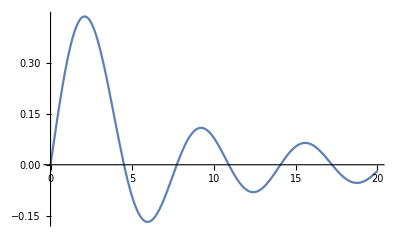

```mathematica
(* Page 29 *)
Plot[SphericalBesselJ[1,x],{x,0,20}]
```

```mathematica
(*Page 29 quation 3.3 *)
Clear[n]
DSolve[f''[r]+2/r f'[r]+f[r]-(n (n+1))/r^2 f[r]==0,f[r],r]
```

{{f[r]→C[1] SphericalBesselJ[n,r]+C[2] SphericalBesselY[n,r]}}

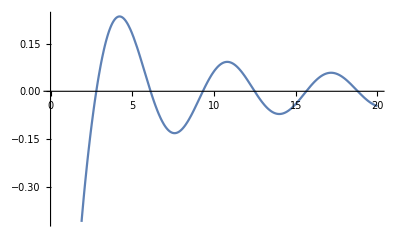

```mathematica
Plot[SphericalBesselY[1,x],{x,0,20}]
```

```mathematica
(* See documentation for asympotics at infinity: 
 https://reference.wolfram.com/language/ref/SphericalBesselJ.html *)

Series[SphericalBesselJ[1,ω r],{ r,Infinity,2}]
```

√(π/2) (Cos[ω r+O[1/r]^3] (-(√(2/π) √r)/(√ω √(r ω) r)+O[1/r]^3)+((√(2/π) √r)/(ω^(3/2) √(r ω) r^2)+O[1/r]^(5/2)) Sin[ω r+O[1/r]^3])

```mathematica
Series[SphericalBesselJ[1,ω r],{r,Infinity,2}] // Normal // PowerExpand
```

√(π/2) (-(√(2/π) Cos[r ω])/(r ω)+(√(2/π) Sin[r ω])/(r^2 ω^2))

```mathematica
Series[SphericalBesselJ[1,ω r],{r,Infinity,2}] // Normal // PowerExpand // ExpToTrig
```

-Cos[r ω]/(r ω)+Sin[r ω]/(r^2 ω^2)

```mathematica
Series[SphericalBesselJ[n,x],{x,Infinity,1}]
```

√(π/2) (Cos[-x+1/2 (1+n) π+O[1/x]^2] ((√(2/π))/x+O[1/x]^2)+O[1/x]^2 Sin[-x+1/2 (1+n) π+O[1/x]^2])

## IMPORTANT Definition of χ Page 33 Equation 3.23 and assorted bad ideas

```mathematica
Clear[χReplace]
ΧReplace = 
χ-> ω ( t-r Sin[γ] Sin[θ] Sin[ϕ] - r Cos[γ] Cos[θ] )
```

χ→ω (t-r Cos[γ] Cos[θ]-r Sin[γ] Sin[θ] Sin[ϕ])

```mathematica
Clear[xRotation]
xRotation = 
({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[γ], -Sin[γ]}, {0, 0, Sin[γ], Cos[γ]}});
xRotation // MatrixForm // pdConv
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | cos(γ) | -sin(γ)
0 | 0 | sin(γ) | cos(γ))

```mathematica
(* Page 40, no idea how they're doing this rotation *)

Clear[hμν]
hμν=
 ({{0, 0, 0, 0}, {0, Cos[χ], Sin[χ], 0}, {0, Sin[χ], -Cos[χ], 0}, {0, 0, 0, 0}});
hμν // MatrixForm //  pdConv
```

(0 | 0 | 0 | 0
0 | cos(χ) | sin(χ) | 0
0 | sin(χ) | -cos(χ) | 0
0 | 0 | 0 | 0)

```mathematica
xRotation . hμν  // MatrixForm
```

{{0,0,0,0},{0,Cos[χ],Sin[χ],0},{0,Cos[γ] Sin[χ],-Cos[γ] Cos[χ],0},{0,Sin[γ] Sin[χ],-Cos[χ] Sin[γ],0}}

```mathematica
DSolve[r^2 D[U[r],{r,2}]+ 2 r D[U[r],r] == - n^2 ,U[r],r]
```

{{U[r]→-C[1]/r+C[2]-n^2 Log[r]}}

```mathematica
(* 
DSolve[ D[U[θ],{θ,2}]  + Cot[θ] D[U[θ],θ] ==  n^2 , U[θ],θ]  // FullSimplify 
*)
```

## Previous Attempt

```mathematica
(* Definition of ρ  equation 2.22 page 17 *)

∑_(b=0)^3 ∑_(a=0)^3 ((D[(lcomponents[[a+1]]/. ΔReplace // Expand // Simplify ), variables[[b+1]]]-∑_(c=0)^3 gamma[a,b,c](lcomponents[[c+1]]/. ΔReplace // Expand // Simplify))(mup[[a+1]]/. ΔReplace // Expand // Simplify )(mupbar[[b+1]]/. ΔReplace // Expand // Simplify )) // Expand // Simplify
```

```mathematica
(* Maybe this is β *)

∑_(b=0)^3 ∑_(a=0)^3 ((D[(lcomponents[[a+1]]/. ΔReplace // Expand // Simplify ), variables[[b+1]]]-∑_(c=0)^3 gamma[a,b,c](lcomponents[[c+1]]/. ΔReplace // Expand // Simplify ))nup[[a+1]]mup[[b+1]])-
∑_(b=0)^3 ∑_(a=0)^3 ((D[(mcomponents[[a+1]]/. ΔReplace // Expand // Simplify ), variables[[b+1]]]-∑_(c=0)^3 gamma[a,b,c](mcomponents[[c+1]]/. ΔReplace // Expand // Simplify ))mupbar[[a+1]]mup[[b+1]]) // Expand // Simplify
```

```mathematica
(* Maybe this is the definition of π equation 2.22 *)
(-1)*∑_(b=0)^3 ∑_(a=0)^3 ((D[ncomponents[[a+1]], variables[[b+1]]]-∑_(c=0)^3 gamma[a,b,c]ncomponents[[c+1]])mupbar[[a+1]]lup[[b+1]]) /. ΔReplace  // Expand // Simplify
```

```mathematica
(* Maybe this is τ *)

∑_(b=0)^3 ∑_(a=0)^3 ((D[lcomponents[[a+1]], variables[[b+1]]]-∑_(c=0)^3 gamma[a,b,c]lcomponents[[c+1]])mup[[a+1]]nup[[b+1]]) // Expand  // Simplify
```

```mathematica
(* Maybe this is μ *)

(-1)*∑_(b=0)^3 ∑_(a=0)^3 ((D[ncomponents[[a+1]], variables[[b+1]]]-∑_(c=0)^3 gamma[a,b,c]ncomponents[[c+1]])mupbar[[a+1]]mup[[b+1]]) // Simplify
```

```mathematica
(* Maybe this is γ *)

∑_(b=0)^3 ∑_(a=0)^3 ((D[lcomponents[[a+1]], variables[[b+1]]]-∑_(c=0)^3 gamma[a,b,c]lcomponents[[c+1]])nup[[a+1]]nup[[b+1]])-
∑_(b=0)^3 ∑_(a=0)^3 ((D[mcomponents[[a+1]], variables[[b+1]]]-∑_(c=0)^3 gamma[a,b,c]mcomponents[[c+1]])mupbar[[a+1]]n[[b+1]]) // Expand // Simplify
```

```mathematica
(* Maybe this is α *)

∑_(b=0)^3 ∑_(a=0)^3 ((D[lcomponents[[a+1]], variables[[b+1]]]-∑_(c=0)^3 gamma[a,b,c]lcomponents[[c+1]])nup[[a+1]]mupbar[[b+1]])-
∑_(b=0)^3 ∑_(a=0)^3 ((D[mcomponents[[a+1]], variables[[b+1]]]-∑_(c=0)^3 gamma[a,b,c]mcomponents[[c+1]])mupbar[[a+1]]mbar[[b+1]]) /. ΔReplace  // Expand // Simplify
```

```mathematica
metric2pt18 // MatrixForm
```

(-1+(2 M r)/Σ[r,θ] | 0 | 0 | -(2 a M r z[θ]^2)/Σ[r,θ]
0 | Σ[r,θ]/Δ[r] | 0 | 0
0 | 0 | Σ[r,θ] | 0
-(2 a M r z[θ]^2)/Σ[r,θ] | 0 | 0 | z[θ]^2 (a^2+r^2+(2 a^2 M r z[θ]^2)/Σ[r,θ]))

```mathematica
Table[-ℓ[[μ]] 𝓃[[ν]]-𝓃[[μ]] ℓ[[ν]]+𝓂[[μ]] 𝓂bar[[ν]]+𝓂bar[[μ]] 𝓂[[ν]] , {μ,1,4},{ν,1,4}]  // Expand // FullSimplify // MatrixForm
```

((-(a^2+r^2)^2+a^2 z[θ]^2 Δ[r])/((a^2+r^2-a^2 z[θ]^2) Δ[r]) | 0 | 0 | -(a (a^2+r^2-Csc[θ] z[θ] Δ[r]))/((a^2+r^2-a^2 z[θ]^2) Δ[r])
0 | Δ[r]/(a^2+r^2-a^2 z[θ]^2) | 0 | 0
0 | 0 | 1/(a^2+r^2-a^2 z[θ]^2) | 0
-(a (a^2+r^2-Csc[θ] z[θ] Δ[r]))/((a^2+r^2-a^2 z[θ]^2) Δ[r]) | 0 | 0 | (-a^2+Csc[θ]^2 Δ[r])/((a^2+r^2-a^2 z[θ]^2) Δ[r]))